```mathematica
Clear[u];
```

```mathematica
diffPD1 = {cA''[u]== -phiA^2*cA[u],cA[0]==0.1, cA[1]==0.1};
solPD1 = DSolve[diffPD1, cA[u],u]
```

{{cA[u]→0.1 Cos[0.324443 u]+0.016366 Sin[0.324443 u]}}

```mathematica
diffPD2 = {cB''[u]==-phiB^2*cB[u]+phiA^2*cA[u],cB[0]==0, cB[1]==0}
solPD2= DSolve[diffPD2, cB[u],u]
```

{cB''[u]==0.105263 cA[u]-0.0263158 cB[u],cB[0]==0,cB[1]==0}

{{cB[u]→1. Sin[0.162221 u] 0.648886 cA[K[2]] Cos[0.162221 K[2]]K[2]1u-1. Cos[0.162221 u] -0.648886 cA[K[1]] Sin[0.162221 K[1]]K[1]10+6.11025 Sin[0.162221 u] -0.648886 cA[K[1]] Sin[0.162221 K[1]]K[1]10+1. Cos[0.162221 u] -0.648886 cA[K[1]] Sin[0.162221 K[1]]K[1]1u}}

```mathematica
L=0.001;
```

```mathematica
kA= 2;
kB = 0.5;
Deff= 1.9*10^(-5);
```

```mathematica
phiA=L*(kA/Deff)^0.5;
phiB=L*(kB/Deff)^0.5;
```

```mathematica
Exit[]
```

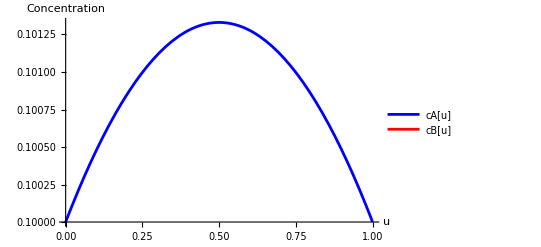

```mathematica
Plot[{Evaluate[cA[u]/. solPD1[[1]]],Evaluate[cB[u]/. solPD2[[1]]]},{u,0,1},PlotLegends->{"cA[u]","cB[u]"},AxesLabel->{"u","Concentration"},PlotStyle->{Blue,Red}]
```